# DFT 学习

### 绘制随机的实数列表l

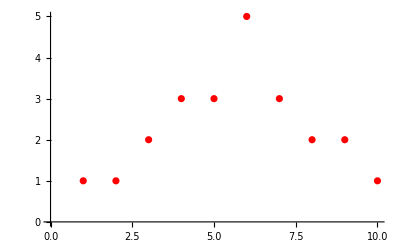

```mathematica
l={1,1,2,3,3,5,3,2,2,1};
len=Length[l]; 
lp=ListPlot[l,PlotStyle->Red]
```

### 计算该列表的离散傅里叶变换，并绘图

```mathematica
f=Fourier[l]
```

{7.27324+0. ⅈ,-2.38597+0.30075 ⅈ,0.376622-0.185874 ⅈ,-0.618198-0.185874 ⅈ,0.730175+0.30075 ⅈ,-0.316228+0. ⅈ,0.730175-0.30075 ⅈ,-0.618198+0.185874 ⅈ,0.376622+0.185874 ⅈ,-2.38597-0.30075 ⅈ}

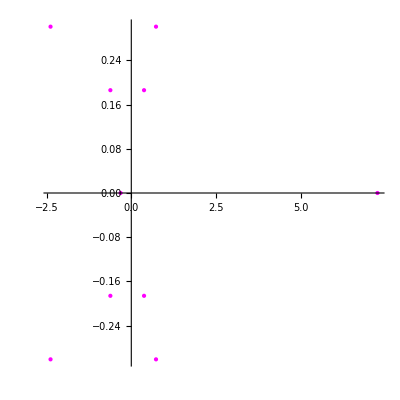

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@f,AspectRatio->1,PlotStyle->{PointSize[Large],Magenta}]
```

### 计算每个信号分量，并分别绘图

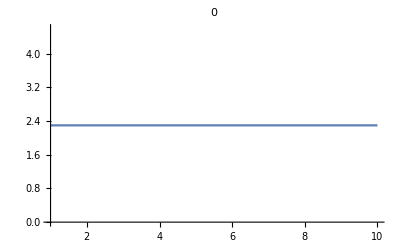
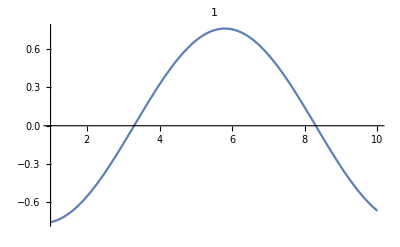
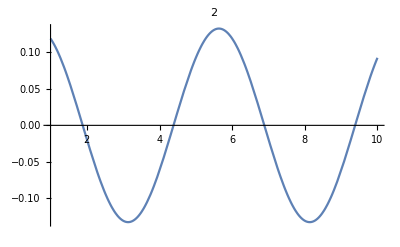
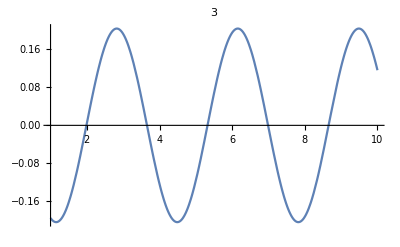
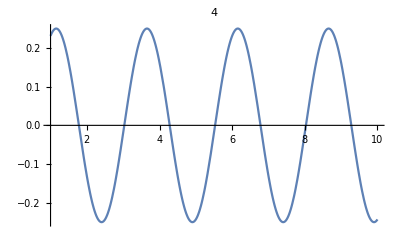
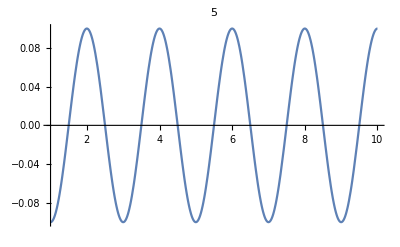
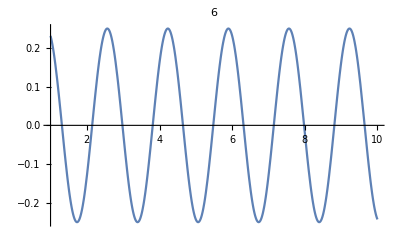
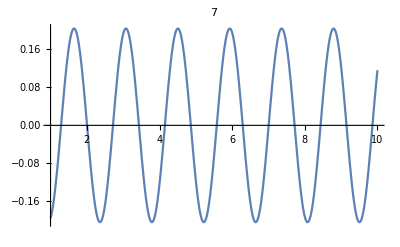
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
funcs=Table[Norm[f[[n]]]/(√len)Cos[((n-1)2π)/len(t-1)-Arg[f[[n]]]],{n,len}];
Partition[Table[Plot[funcs[[r]],{t,1,len},PlotLabel->r-1],{r,len}],UpTo@4]//Grid
```

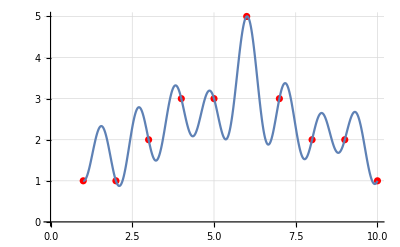

```mathematica
Show[lp,Plot[Total@funcs,{t,1,len}],GridLines->Automatic]
```

### 将上面过程包装成函数

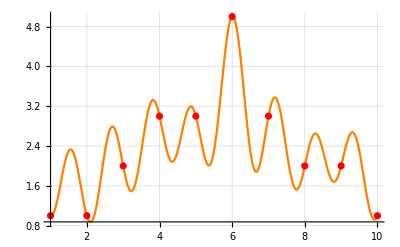

```mathematica
draw[l_]:=Block[{len=Length[l],f=Fourier[l],func},func=Sum[Norm[f[[r]]]/(√len)Cos[(2π(r-1))/len(t-1)-Arg[f[[r]]]],{r,len}];Show[Plot[func,{t,1,len},PlotStyle->Orange,PlotRange->All],
ListPlot[l,PlotStyle->Red],GridLines->Automatic]]
draw[l]
```

### 上面的图形问题在于错把有初相的低频基信号当成高频

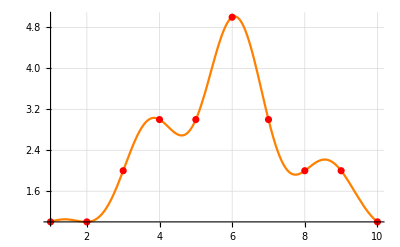

```mathematica
draw22[l_]:=Block[{len=Length[l],f=Fourier[l],func,k},k=Ceiling[len/2];func=Sum[c=f[[Mod[n+len,len]+1]];Norm[c]/(√len)Cos[(2π n)/len(t-1)-Arg[c]],{n,k-len,k-1}];Show[Plot[func,{t,1,len},PlotStyle->Orange,PlotRange->All],
ListPlot[l,PlotStyle->Red],GridLines->Automatic]]
draw22[l]
```

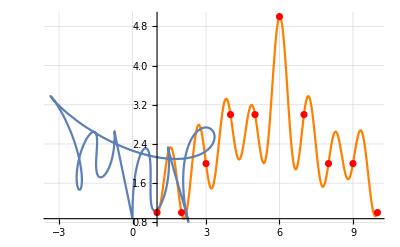

```mathematica
draw33[l_]:=Block[{len=Length[l],f=Fourier[l],func},func=Sum[Norm[f[[r]]]/(√len)Cos[(2π(r-1))/len(t-1)-Arg[f[[r]]]],{r,len}];
m=8;
cn=Table[1/(2π)Integrate[(t+I func) Exp[-I k t],{t,-π,π}],{k,-m,m}];
p=Sum[cn[[n]]Exp[(n-m-1)I t],{n,2m+1}];
Show[Plot[func,{t,1,len},PlotStyle->Orange],
ParametricPlot[ReIm@p,{t,0,2π}],
ListPlot[l,PlotStyle->Red],GridLines->Automatic,PlotRange->All]]
draw33[l]
```

### 使用随机数列对比观察

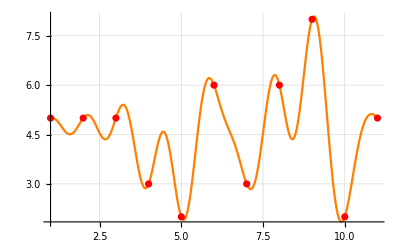

```mathematica
draw[{5,5,5,3,2,6,3,6,8,2,5}]
```

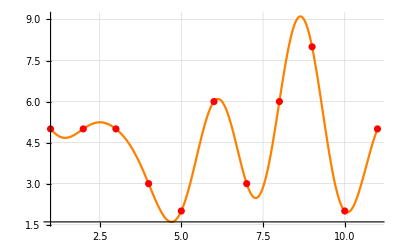

```mathematica
draw22[{5,5,5,3,2,6,3,6,8,2,5}]
```

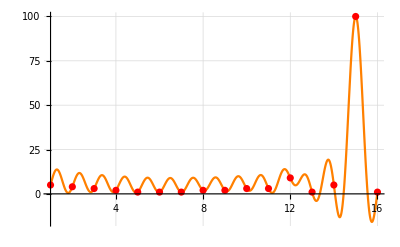

```mathematica
draw[{5,4,3,2,1,1,1,2,2,3,3,9,1,5,100,1}]
```

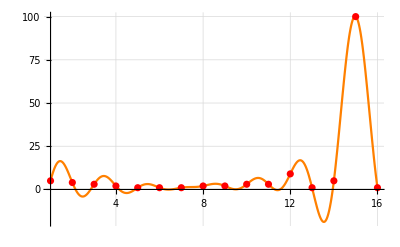

```mathematica
draw22[{5,4,3,2,1,1,1,2,2,3,3,9,1,5,100,1}]
```

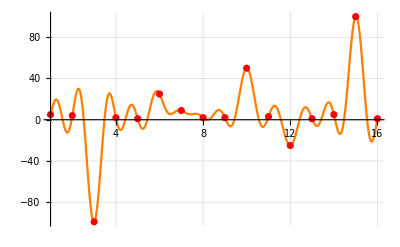

```mathematica
draw[{5,4,-99,2,1,25,9,2,2,50,3,-25,1,5,100,1}]
```

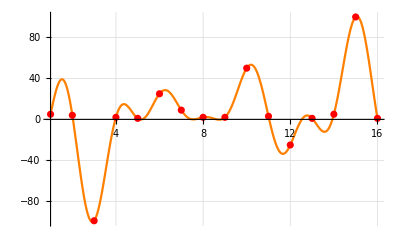

```mathematica
draw22[{5,4,-99,2,1,25,9,2,2,50,3,-25,1,5,100,1}]
```

### 以sin(4π x)信号的k个采样点为例，对比观察

```mathematica
k=20;
s=Table[Sin[2*2π(n-1)/k],{n,k}]
```

{0,√(5/8-(√5)/8),√(5/8+(√5)/8),√(5/8+(√5)/8),√(5/8-(√5)/8),0,-√(5/8-(√5)/8),-√(5/8+(√5)/8),-√(5/8+(√5)/8),-√(5/8-(√5)/8),0,√(5/8-(√5)/8),√(5/8+(√5)/8),√(5/8+(√5)/8),√(5/8-(√5)/8),0,-√(5/8-(√5)/8),-√(5/8+(√5)/8),-√(5/8+(√5)/8),-√(5/8-(√5)/8)}

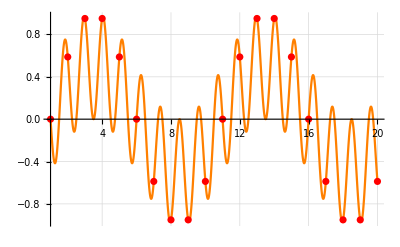

```mathematica
draw[s]
```

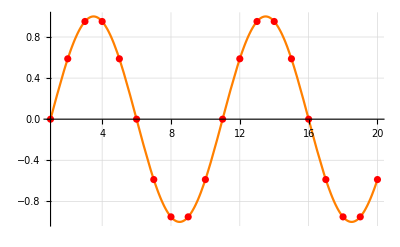

```mathematica
draw22[s]
```

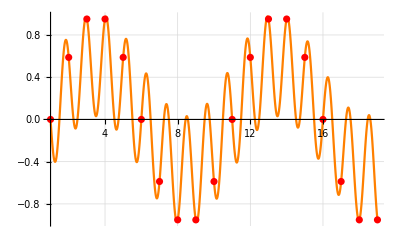

```mathematica
draw[s[[;;-2]]]
```

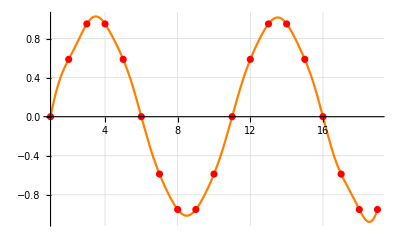

```mathematica
draw22[s[[;;-2]]]
```

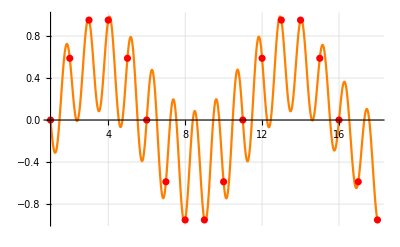

```mathematica
draw[s[[;;-3]]]
```

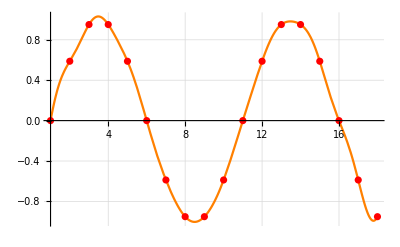

```mathematica
draw22[s[[;;-3]]]
```

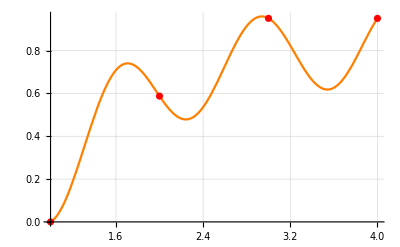

```mathematica
draw[s[[;;4]]]
```

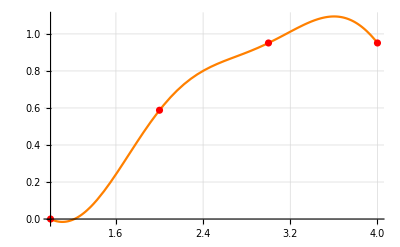

```mathematica
draw22[s[[;;4]]]
```